Import Data

```mathematica
streckeTreppe = 9.39;
```

```mathematica
dataPath="../data/2017/Messungen_2017_Geschwindigkeit_Treppe_Auf.csv";
dataTreppeAuf=SemanticImport@FileNameJoin@{NotebookDirectory[],dataPath}
```

Dataset[<>]

```mathematica
dataTreppeMitGeschw = dataTreppeAuf[All,Append[#,"Geschwindigkeit"->streckeTreppe/#Zeit]&]
```

Dataset[<>]

## Histogramm

Es wird ein Histogramm erstellt und einer Normalverteilung gegenübergestellt. Für die Kurve der Normalverteilung muss der Erwartungswert und die Standardabweichung berechnet werden.

Berechnung des Mittelwertes und der Standardabweichung

```mathematica
geschwMean = Mean[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

0.877019

```mathematica
geschwDeviation = StandardDeviation[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

0.158964

Gegenüberstellung von Häufigkeitsverteilung und Normalverteilung. 
ACHTUNG: Das Histogramm wurde mit der Option “PDF” erstellt. Das bedeutet, dass nicht die absoluten Häufigkeiten sondern die Häufigkeitsdichte dargstellt ist, Damit lässt es sich besser mit dem Graphen der Normalverteilung vergleichen. Die Darstellung ist dann nicht mehr von der Anzahl der säulen abhängig.
Bemerkungen wie getrödelt wurden ignoriert. Es wird angenommen, dass im Schnitt es immer Personen gibt, die langsamer oder schneller gehen. Die Probanden hatten keine Vorgabe eine bestimmte Geschwindigkeit einzuhalten. Somit sind auch Probanden zu berücksichtigen, die langsamer gehen. Es ist jedoch anzumerken, dass bei einem Versuch mit nur einer geringen Anzahl von Probanden, solche Sonderheiten eventuell eine signifikante Abweichung verursachen.


ACHTUNG: Die Ausreisser in diesem Datensatz sind periodisch. Das heißt es gibt 4 Personen, welche immer schneller gehen, als der Rest. Es ist anzunehmen, dass dies die Auswertung stark beeinflussen wird.

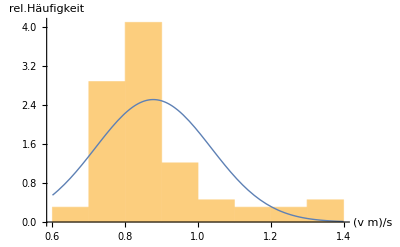

```mathematica
Show[Histogram[dataTreppeMitGeschw[All, "Geschwindigkeit"],10, "PDF"],Plot[PDF[NormalDistribution[geschwMean,geschwDeviation],x],{x,0.6,1.4},PlotStyle->Thick], AxesLabel->{HoldForm[(v m)/s],HoldForm[rel.Häufigkeit]}]
```

## Quantileplot

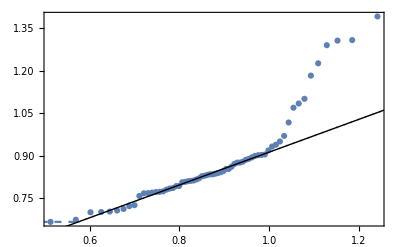

```mathematica
QuantilePlot[dataTreppeMitGeschw[All, "Geschwindigkeit"]]
```

## Distribution Fit Test

```mathematica
DistTestTreppe=DistributionFitTest[Array[dataTreppeMitGeschw[All, "Geschwindigkeit"], 66],NormalDistribution[geschwMean,geschwDeviation],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppe["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 3.67396 | 0.0126832
Baringhaus-Henze | 4.53865 | 0.000403182
Cramér-von Mises | 0.638786 | 0.0179638
Jarque-Bera ALM | 45.2212 | 0.000864057
Mardia Combined | 45.2212 | 0.000864057
Mardia Kurtosis | 3.44345 | 0.000574336
Mardia Skewness | 26.5574 | 2.55817×10^-7
Pearson χ^2 | 25. | 0.00534551
Shapiro-Wilk | 0.835009 | 4.31299×10^-7

Der Distribution Fit Test ergibt, dass die Geschwindigkeiten NICHT normalverteilt sind. Laut dem Cramer-von Mises Test wird die 5% Hürde nicht überschritten.
Die Geschwindigkeiten Beim Raufgehen der Treppen sind nicht normalverteilt.

## Ausreißer entfernen

Es wurde festgestellt, dass die Geschwindigkeiten nicht normalverteilt sind. Es wird untersucht, ob die Ausreißer einen signifikanten Einfluss ausüben.

```mathematica
dataOhneAusreisser = dataTreppeMitGeschw[Select[#"Bemerkung"==""&], "Geschwindigkeit"]
```

Dataset[<>]

```mathematica
geschwNeuMean = Mean[dataOhneAusreisser]
```

0.814919

```mathematica
geschwNeuDeviation = StandardDeviation[dataOhneAusreisser]
```

0.0691465

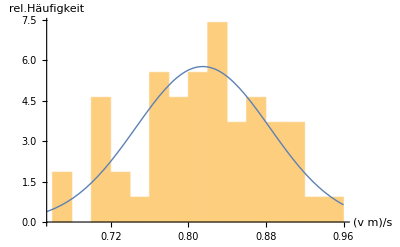

```mathematica
Show[Histogram[dataOhneAusreisser,10, "PDF"],Plot[PDF[NormalDistribution[geschwNeuMean,geschwNeuDeviation],x],{x,0.65,0.96},PlotStyle->Thick],AxesLabel->{HoldForm[(v m)/s],HoldForm[rel.Häufigkeit]}]
```

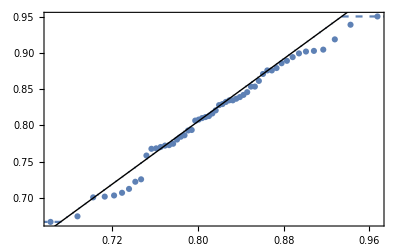

```mathematica
QuantilePlot[dataOhneAusreisser]
```

```mathematica
DistTestTreppeOhneAusreisser=DistributionFitTest[Array[dataOhneAusreisser, 54],NormalDistribution[geschwNeuMean,geschwNeuDeviation],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
DistTestTreppeOhneAusreisser["TestDataTable",All]
```

| Statistic | P-Value
Anderson-Darling | 0.33829 | 0.90645
Baringhaus-Henze | 0.213705 | 0.858651
Cramér-von Mises | 0.0421682 | 0.921661
Jarque-Bera ALM | 1.31475 | 0.440072
Mardia Combined | 1.31475 | 0.440072
Mardia Kurtosis | -0.891517 | 0.372652
Mardia Skewness | 0.553342 | 0.456956
Pearson χ^2 | 12.2963 | 0.197116
Shapiro-Wilk | 0.977864 | 0.414303

Es ist festzustellen, dass die Geschwindigkeiten normalverteilt sind, wenn die Ausreißer nicht berücksichtigt werden. Für spätere betrachtung muss entschieden werden, ob diese Ausreisser in die Auswertung mit einfließen oder nicht.